```mathematica
ClearAll["Global'*"];
Needs["PlotLegends`"](* PlotLegends is now obsolete*) 
Evaluate[{FileNameSetter[Dynamic[datafilename1]],Dynamic[datafilename1]}] 
If[FileExistsQ[datafilename1],Print["File exists "datafilename1],Print["This File does not exist"];Quit[]];
 data1=Import[datafilename1];

memoryTem=0;
mtxw=320; mtxh=240; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;

ImageSizeLocal=450;
colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};

For[i=1,i≤mtxw,i++,{
For[j=1,j≤Round[mtxh/2],j++,{
memoryTem=data1[[(i-1)*mtxh+j,3]];
data1[[(i-1)*mtxh+j,3]]=data1[[(i-1)*mtxh+(mtxh+1-j),3]];(*5*RandomReal[]*(-1)^RandomInteger[1]*);
data1[[(i-1)*mtxh+(mtxh+1-j),3]]=memoryTem(*5*RandomReal[]*(-1)^RandomInteger[1]*);
}]
}]
Print["CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}"]
(*ListDensityPlot[data1,PlotRange->All,ColorFunction->colorsGoody(*GrayLevel*),Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Placed[Automatic,Below],ColorFunctionScaling->True,InterpolationOrder->0] *)

Mask43=ArrayReshape[Transpose@ArrayReshape[ArrayReshape[Transpose@ArrayReshape[Table[i,{i,mtxw*mtxh}],{mtxw,mtxh}],{redw,mtxh,sw}],{mtxh,redw,sw}],{redw,redh,sw*sh}];

If[Mask43[[redw,redh,sw*sh]]==mtxw*mtxh,Print["CheckPoint#2  - excellent"],Print["CheckPoint#2 - failed!"]]

data2=data1; Clear[data1];
arrenged=Array[{#/#}&,{redw,redh,3}];

For[i=1,i<=Length[arrenged],i++,{
For[j=1,j<=Length[arrenged[[i]]],j++,{
arrenged[[i,j,1]]=(i-0.5)*sw;
arrenged[[i,j,2]]=sh*(j-0.5);

arrenged[[i,j,3]]=Sum[data2[[Mask43[[i,j,a]],3]],{a,sw*sh}]*(1/(sw*sh));
(*noiseF[x_,av_]:=x-av;
For[a:=1,a≤(sw*sh),a++,{data2[[Mask43[[i,j,a]],3]]=(1/TechError)*noiseF[data2[[Mask43[[i,j,a]],3]],arrenged[[i,j,3]]];
If[Abs@data2[[Mask43[[i,j,a]],3]]>FilterForErrorMagnitude1,data2[[Mask43[[i,j,a]],3]]=0];
data2[[Mask43[[i,j,a]],3]]=Sqrt[(1/(sw*sh))*(TechError*data2[[Mask43[[i,j,a]],3]])^2];

}]*)

  }]

}]
arrengedList=ArrayReshape[arrenged,{Length[arrenged]*Length[arrenged[[1]]],3}];

ListDensityPlot[arrengedList,PlotRange->All,ColorFunction->colorsGoody(*GrayLevel*),ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Placed[Automatic,Below],ColorFunctionScaling->True,InterpolationOrder->0]
Clear[arrenged,arrengedList,Mask43];
(*For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>Temperaturethreshold,data2[[i,3]]=0]]
For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>0.1,data2[[i,3]]=Temperaturethreshold]]*)

(*ListDensityPlot[data2,PlotRange->All,ColorFunction->(*colorsGoody*)GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0]*)
(*ListPointPlot3D[data1,ColorFunction->Function[{x,y,z},Hue[-z]]]*)

Clear[data2];
```

{,}

C:\A\Notes\PRG\W\Fractals\gjIR000110.dat File exists

CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}

CheckPoint#2  - excellent

-Graphics-

```mathematica
Import["C:\\A\\Universal\\1\\#2\\Fractacls\\FDE\\FDE_SimRF2D\\colored1.bmp"]
```

```mathematica
ColorConvert[,"GrayLevel"]
```

```mathematica
({{a, b, c, d}}).({{1, 0}, {1, 0}, {0, 1}, {0, 1}})
```

{{a+b,c+d}}

```mathematica
a={{1,1,1,1},{1,1,1,1}};
b={{1,1,0,0},{0,0,1,1}};
a.b
```

{{1,1,1,1},{1,1,1,1}}.{{1,1,0,0},{0,0,1,1}}

{w,ww,www,wwww}.{{1,1,0,0},{0,0,1,1}}

```mathematica
({{k, l}, {m, n}}).({{k, l}, {m, n}})//MatrixForm
```

(k^2+l m | k l+l n
k m+m n | l m+n^2)

```mathematica
({{k, l, m, n}}).({{1, 0, 1, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {01, 0, 0, 1}})//MatrixForm
```

(k+n | 0 | k+m | n)

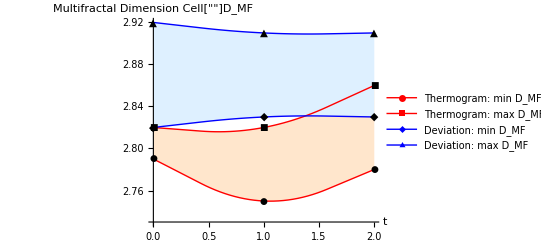

```mathematica
Dthermmin={{0,2.79},{1,2.75},{2,2.78 }};
Dthermmax={{0,2.82},{1,2.82},{2,2.86 }};
Dnoisemin={{0,2.82},{1,2.83},{2,2.83 }};
Dnoisemax={{0,2.92},{1,2.91},{2,2.91 }};
ListLinePlot[{Dthermmin,Dthermmax,Dnoisemin,Dnoisemax}, PlotStyle->{Red,Red,Blue,Blue},AxesLabel->{t,"Multifractal Dimension Cell[""]D_MF"},AxesStyle->Directive[Black,FontFamily->"Helvetica",FontSize->12], Mesh->Full,MeshStyle->PointSize[Medium],PlotMarkers->Automatic,InterpolationOrder->2,PlotLegends->LineLegend[{"Thermogram: min D_MF","Thermogram: max D_MF", "Deviation:  min D_MF","Deviation:  max D_MF"},LegendMarkerSize->10,LegendFunction->Frame],Filling->{4->{{3},LightBlue},2->{{1},LightOrange}}]
```

```mathematica
Dthermmin={{0,2.79},{1,2.75},{2,2.78 }};
ListLinePlot[{Dthermmin,Dthermmax,Dnoisemin,Dnoisemax}, PlotStyle->{Red,Red,Blue,Blue},AxesLabel->{t,"Multifractal Dimension Cell[""]D_MF"},AxesStyle->Directive[Black,FontFamily->"Helvetica",FontSize->12], Mesh->Full,MeshStyle->PointSize[Medium],PlotMarkers->Automatic,InterpolationOrder->2,PlotLegends->LineLegend[{"Thermogram: min D_MF","Thermogram: max D_MF", "Noise:  min D_MF","Noise:  max D_MF"},LegendMarkerSize->10,LegendFunction->Frame],Filling->{4->{{3},LightBlue},2->{{1},LightOrange}}]
```

```mathematica
-Graphics-//Image
```

```mathematica
//Image
```

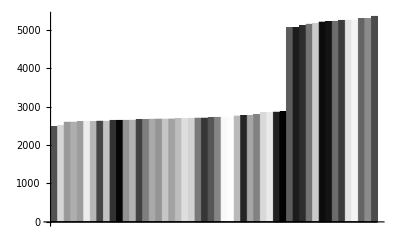

```mathematica
colorquantized=SortBy[Tally[Flatten[ImageData[ColorQuantize[-Graphics-,50,Dithering->False]],1]],Last];

BarChart[colorquantized[[All,2]],ChartStyle->RGBColor/@colorquantized[[All,1]]]
```

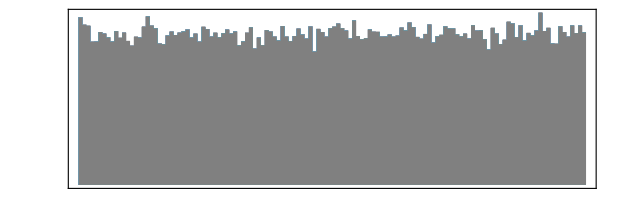

```mathematica
ImageHistogram[-Graphics-]
```

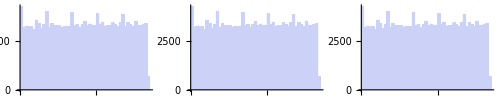

| Mean | StDev
Red | 0.501314 | 0.290286
Blue | 0.501314 | 0.290286
Green | 0.501314 | 0.290286

```mathematica
img=-Graphics-;
imgChannelsRGB=Transpose@Flatten[ImageData[img],1];
GraphicsRow[Histogram/@imgChannelsRGB,ImageSize->500]
TableForm[Through[{Mean,StandardDeviation}[#]]&/@imgChannelsRGB,TableHeadings->{{"Red","Blue","Green"},{"Mean","StDev"}}]
```

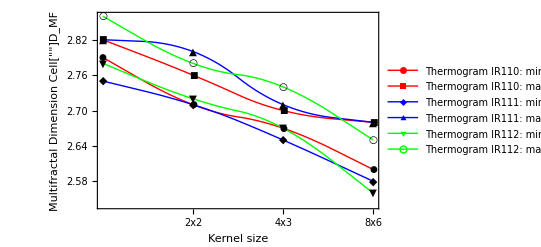

```mathematica
Dtherm1min={{0, 2.79},{1,2.71},{2,2.67},{3,2.60 }};
Dtherm1max={{0, 2.82},{1,2.76},{2,2.70},{3,2.68 }};
Dtherm2min={{0, 2.75},{1,2.71},{2,2.65},{3,2.58 }};
Dtherm2max={{0, 2.82},{1,2.80},{2,2.71},{3,2.68 }};
Dtherm3min={{0, 2.78},{1,2.72},{2,2.67},{3,2.56 }};
Dtherm3max={{0, 2.86},{1,2.78},{2,2.74},{3,2.65 }};
ListLinePlot[{Dtherm1min,Dtherm1max,Dtherm2min,Dtherm2max,Dtherm3min,Dtherm3max}, PlotStyle->{{Red, Medium},{Red, Medium},{Blue, Medium},{Blue, Medium},{Green, Medium},{Green, Medium}},FrameLabel->{"Kernel size","Multifractal Dimension Cell[""]D_MF"},Frame->True ,FrameStyle->Directive[Black,FontFamily->"Helvetica",FontSize->12],FrameTicks->{{All,None},{{{0," ",.05},{1,"2x2",.05},{2,"4x3",.05},{3,"8x6",.05}},None}}, Mesh->Full,MeshStyle->PointSize[Medium],PlotMarkers->Automatic,InterpolationOrder->2,PlotLegends->LineLegend[{"Thermogram IR110: min D_MF","Thermogram IR110: max D_MF", "Thermogram IR111: min D_MF","Thermogram IR111: max D_MF","Thermogram IR112: min D_MF","Thermogram IR112: max D_MF"},LegendMarkerSize->10,LegendFunction->Frame],Filling->{4->{{3},None},2->{{1},None}}]
```

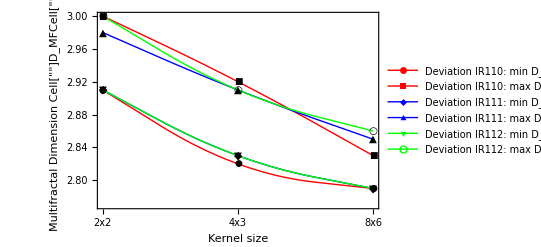

```mathematica
Dtherm1min={{0,2.91},{1,2.82},{2,2.79 }};
Dtherm1max={{0,3.00},{1,2.92},{2,2.83 }};
Dtherm2min={{0,2.91},{1,2.83},{2,2.79}};
Dtherm2max={{0,2.98},{1,2.91},{2,2.85 }};
Dtherm3min={{0,2.91},{1,2.83},{2,2.79 }};
Dtherm3max={{0,3.00},{1,2.91},{2,2.86 }};
ListLinePlot[{Dtherm1min,Dtherm1max,Dtherm2min,Dtherm2max,Dtherm3min,Dtherm3max}, PlotStyle->{{Red, Medium},{Red, Medium},{Blue, Medium},{Blue, Medium},{Green, Medium},{Green, Medium}},FrameLabel->{{"Multifractal Dimension Cell[""]D_MFCell[""]",None},{"Kernel size","Filtered by ∆ (*Cell[GraphicsData["Metafile", "\<\
CF5dJ6E]HGAYHf4PEfU^I6mgLb15CDHPAVmbKF5d0@0000fD0@0006`000000000kooooe@0001[0000
00000000001b0@00Y`400215CDH00040U0d004P0000500000000000000000000A18009hJ00360000
8040000000000000000003l50`3<IP@0AP0002`0000P0000ADe6:`500@0L00004000008@`=/00000
F08005P200160000G00005000015CDH[8T0400`0000000007T0900`000000000940100`000000000
<4020100000400000020?b501`0<0000000000A0000<0000000001H0000<0000600000X0000@0000
oooooocoool90000400005D0001V0000DP00070100010000Y?ooo`0000000000000009010000003<
14008T<0H@1/06T0HP1b06T000000000000000000000000000000000000000000000000000000000
00000000000000000000000000000000000000000000000000000000000000000000000000000000
l;DZ08Rg:P1`RbH59;@Z0?AOb5f8]bX0800007bd:P3oooooK;LZ00Be:P15n]5MO;@Z08Rg:P0P0000
ooooooa6C@6jn]5M0@000000001H0P009@0003L^T07<008?1@820P@30PCo0P3Qoj`0@0T000000000
W`40000000130640K01Y0680LP000000000000000000000000000:bd:P2F@l]M20000?ooomoX]2X0
4Vc9GObd:P20/KeN5;DZ0?a6C@4PATd1I7H02000000U000030000040000U000030000040000U0000
30000040000B000030000040000H000030000000009D0000E000004000040000=P0006L000010000
7827@3m0Qd000000E`000040001<00001000000000000000F00006@0001@0000800B03H0000H0000
3000000000960000:00001`00017A4U30P000?gooookooooE00006<000000000AP0001@200080P00
ADe6:bY0000T000060000000P3l000200000P000P3l0080o0020@2501@0<0000000000Q000E`0@00
I040008@`=/200000P0003X1003GcLJJ00000000@0600@<900000=9N000100T000>M00000P0L0000
000500002@8000001@0000810@0000D000010_ooo`050000;P4H00001@0000/2000000D0000<0X01
@04B00009PH?01X0ooooo`0040000<3ooooVoooo004006H1000;00009PH?00`0CF5dJ5AiL6D00200
70000?/2P?h00000002@0@0000840P0@DgU]HVm/07J790Y]l=La053P4P2ZBAMf@94JMS8XIR/40000
;@4000P0000b2T01=0010000XgT:00009PH?00X0ooooo`40000001`0003k0Q001`000000_080003<
0@828U=iLgAUK@00<RQV:`002P0h08X100000?oooom/hQ80100002d10@040000l04000<000000000
240122@0000H00000Q30f`400003000000000000000000006d000400000d00000@00008000000000
00000000X4<00<130`00061EUKl00530ZJZW@P00D<1PEIFoZ:[5@R4000080000HP0000`000010000
2P000100000000000000024000080000HP0000`0000100004@0000`0000800002P00010000000000
000000T0000@0000@0400801000<000040000000000100002`000100001E0000IP00024000080000
9@0000`0000700209@0000`0000000205P0000`000000000600000`0000000006@0000`0003oool0
500000`0000=0000DP00070100020000Y?ooo`0000000000000009010000003<1d008T<0H@1/06T0
HP1b06T0000000000000000000000000000000000000000000000000000000000000000000000;01
mN<GMP0000000000000000000000000000000000003ooooo00000000000000000000000000000000
000000000000000000000000000000000@000?ooool000000000000000000000H1e7000`Q`4L6R6N
402@0@00000000000000000000000000000000000000000000000000000000000000000000000000
000000000000000000000000000000000000000000000000MboBMd2RhTP00000W04o0000?`3TT489
Z1I82BH0KP0X/ch4I7H02000000U000030000080000H000030000000000B000030000040000I0000
30000?ooo`0F0000300001P0000:000040000000000000002@00010000100@00P0400580001`0@00
0`00083nool0000000000000002@0@0000000PL2011C07T0K@1R06l0K00000000000000000000000
000000000000000000000000000000000000000000000000000GMXBR:P2jj1Mf0P0001`J8IhI0;01
mN<GMP0`Q`410000k:HZ0=Xabed8000003270@40002hX2X0@94JM_B[5WK?ZaIf^:0Z06@100000000
00000<PiQPP4000000000><L2R5PXRX0AZ`FMU2/5WH000000000000000000000H1e70000000L6R6N
ha`:8@80002Toooo0000000000000000T04000000<`7@00R@`1Q06`0J@1R07800000000000000000
00000000000000000000000000000000000000000000000000000000/07ehaMf000006Af00P00000
9@0000`000030000E00005@0000>0000koooodD0001[00000@0001ghScm2]8lo=000040100010000
C00000000000000000000?ooooooooooD0000:?`003C0000DP00070100040000400000L000000000
00000;`20000003<1`828U<0N@1c07@0I@1]00000000000000000000000000000000000000000000
0000000000000000000000000000000000000000000001MfQ:8Z0;[X5gH2000071XQWQT0/07ehaMf
03270@40003/YRX0fS7;G@P000000000:P000000003F08<171XQWP0000000000Xo00000000000000
b3V620@000000000ha`:8F2R:P16[1IfD:`FMP000000000000000000001P7DL0000001`J8IkS70XQ
0P000:Coool0000000000000002@0@000000c0M002800640K01Y0680LP0000000000000000000000
000000000000000000000000000000000000000000000000I7H02000000U0000300000@0000X0000
300000<0000U0000300000L0080U000030000000080`0000300000l0080U000030000040001;0000
4000000000050000:00000`0000400009@0000`0000000209@0000`0000700208P0000`0003ooooo
9@0000`0000=0020:00000`0000200008P0000`0003ooooo8P0000`0003oooooAP000700001T0000
ADe6:ba0000T000060000?ooQch000200000P70LR3iPEIFo001@`2Y0000T000060000000P3l00020
0000P000P3l0080o0020@2501`0<0000000000A0000<0000000004H0000D0000200004M4BD<30000
9@0000`0000>00209@0000`0000>0020AP0003@0000X0000ADe6:bY0000T000060000000P3l00020
0000P000P3l0080o0020@24000080000HP0000`0000100002P00010000000000000004`0001T0000
00000040001D0000IP00000000010000E@0006H0000Y0:X0000000000000080o000000000000080o
0000000000000000000000000000000000000000000R000030000?oooom60000700001000015CDH[
0T0000`0000000003P0001@000000000400001@0
\>"], "Graphics",
ImageSize->{14, 16},
ImageMargins->0,

         ImageRegion->{{0., 1.}, {0., 1.}}])0.05К"}},Frame->True ,FrameStyle->Directive[Black,FontFamily->"Helvetica",FontSize->12],FrameTicks->{{All,None},{{{0,"2x2",.05},{1,"4x3",.05},{2,"8x6",.05}},None}}, Mesh->Full,MeshStyle->PointSize[Medium],PlotMarkers->Automatic,InterpolationOrder->2,PlotLegends->LineLegend[{"Deviation IR110: min D_MF","Deviation IR110: max D_MF", "Deviation IR111: min D_MF","Deviation IR111: max D_MF","Deviation IR112: min D_MF","Deviation IR112: max D_MF"},LegendMarkerSize->10,LegendFunction->Frame],Filling->{4->{{3},None},2->{{1},None}}]
```

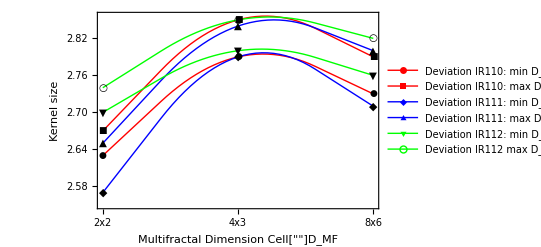

```mathematica
Dtherm1min={{0,2.63},{1,2.79},{2,2.73 }};
Dtherm1max={{0,2.67},{1,2.85},{2,2.79 }};
Dtherm2min={{0,2.57},{1,2.79},{2,2.71}};
Dtherm2max={{0,2.65},{1,2.84},{2,2.80 }};
Dtherm3min={{0,2.70},{1,2.80},{2,2.76 }};
Dtherm3max={{0,2.74},{1,2.85},{2,2.82 }};
ListLinePlot[{Dtherm1min,Dtherm1max,Dtherm2min,Dtherm2max,Dtherm3min,Dtherm3max}, PlotStyle->{Red,Red,Blue,Blue,Green,Green},FrameLabel->{{"Kernel size",None},{"Multifractal Dimension Cell[""]D_MF","Filtered by ∆ >0.05К"}},Frame->True ,FrameStyle->Directive[Black,FontFamily->"Helvetica",FontSize->12],FrameTicks->{{All,None},{{{0,"2x2",.05},{1,"4x3",.05},{2,"8x6",.05}},None}}, Mesh->Full,MeshStyle->PointSize[Medium],PlotMarkers->Automatic,InterpolationOrder->2,PlotLegends->LineLegend[{"Deviation IR110: min D_MF","Deviation IR110: max D_MF", "Deviation IR111: min D_MF","Deviation IR111: max D_MF","Deviation IR112: min D_MF","Deviation IR112 max D_MF"},LegendMarkerSize->10,LegendFunction->Frame],Filling->{4->{{3},None},2->{{1},None}}]
```

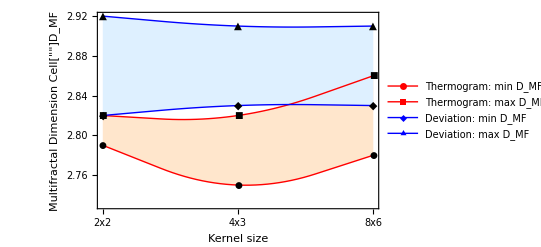

```mathematica
Dthermmin={{0,2.79},{1,2.75},{2,2.78 }};
Dthermmax={{0,2.82},{1,2.82},{2,2.86 }};
Dnoisemin={{0,2.82},{1,2.83},{2,2.83 }};
Dnoisemax={{0,2.92},{1,2.91},{2,2.91 }};

ListLinePlot[{Dthermmin,Dthermmax,Dnoisemin,Dnoisemax}, PlotStyle->{{Red, Medium},{Red,Medium},{Blue,Medium},{Blue,Medium}},PlotMarkers->Automatic,FrameLabel->{{"Multifractal Dimension Cell[""]D_MF",None},{"Kernel size","Deviation filtered by ∆ >0.05К"}},Frame->True ,FrameStyle->Directive[Black,FontFamily->"Helvetica",FontSize->12],FrameTicks->{{All,None},{{{0,"2x2",.05},{1,"4x3",.05},{2,"8x6",.05}},None}}, Mesh->Full,MeshStyle->PointSize[Medium],InterpolationOrder->2,PlotLegends->LineLegend[{"Thermogram: min D_MF","Thermogram: max D_MF", "Deviation:  min D_MF","Deviation:  max D_MF"},LegendMarkers->Automatic,LegendFunction->Frame],Filling->{4->{{3},LightBlue},2->{{1},LightOrange}}]
```

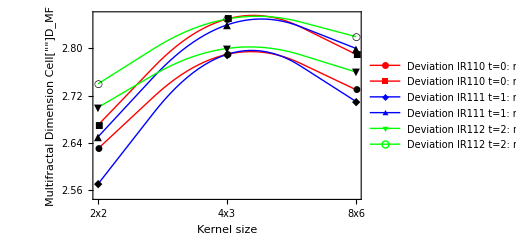

```mathematica
Dtherm1min={{0,2.63},{1,2.79},{2,2.73 }};
Dtherm1max={{0,2.67},{1,2.85},{2,2.79 }};
Dtherm2min={{0,2.57},{1,2.79},{2,2.71}};
Dtherm2max={{0,2.65},{1,2.84},{2,2.80 }};
Dtherm3min={{0,2.70},{1,2.80},{2,2.76 }};
Dtherm3max={{0,2.74},{1,2.85},{2,2.82 }};
ListLinePlot[{Dtherm1min,Dtherm1max,Dtherm2min,Dtherm2max,Dtherm3min,Dtherm3max}, PlotStyle->{{Red, Medium},{Red, Medium},{Blue, Medium},{Blue, Medium},{Green,Medium},{Green, Medium}},FrameLabel->{{"Multifractal Dimension Cell[""]D_MF",None},{"Kernel size","Deviation filtered by ∆ >0.05К"}},Frame->True ,FrameStyle->Directive[Black,FontFamily->"Helvetica",FontSize->12],FrameTicks->{{All,None},{{{0,"2x2",.05},{1,"4x3",.05},{2,"8x6",.05}},None}}, Mesh->Full,MeshStyle->PointSize[Medium],PlotMarkers->Automatic,InterpolationOrder->2,PlotLegends->LineLegend[{"Deviation IR110 t=0: min D_MF","Deviation IR110 t=0: max D_MF", "Deviation IR111 t=1: min D_MF","Deviation IR111 t=1: max D_MF","Deviation IR112 t=2: min D_MF","Deviation IR112 t=2: max D_MF"},LegendMarkerSize->10,LegendFunction->Frame],Filling->{4->{{3},None},2->{{1},None}}]
```

```mathematica
//Image
```